# Problem 3

## Part A

```mathematica
pfunction[xevents_]:=Exp[-lambda]*lambda^xevents/(xevents!);
```

```mathematica
p=Exp[-lambda]*lambda^x/(x!);
```

```mathematica
(* The Mean *)
```

```mathematica
Sum[x*p,{x,0,Infinity}]
```

lambda

```mathematica
(* The Variance *)
```

```mathematica
Sum[(x-lambda)^2*p,{x,0,Infinity}]
```

lambda

## Part B

```mathematica
lambda=5;
```

```mathematica
x=5;
```

```mathematica
N[p]
```

0.175467

```mathematica
N[Integrate[Exp[-lambda]*lambda^xnew/(xnew!),{xnew,0,5}]]
```

0.5275

## Part C

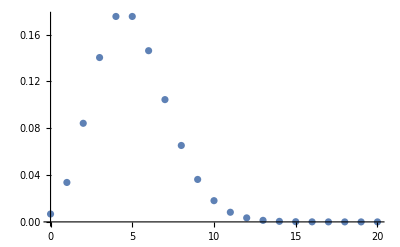

```mathematica
listp={{0,pfunction[0]},{1,pfunction[1]},{2,pfunction[2]},{3,pfunction[3]},{4,pfunction[4]},{5,pfunction[5]},{6,pfunction[6]},{7,pfunction[7]},{8,pfunction[8]},{9,pfunction[9]},{10,pfunction[10]},{11,pfunction[11]},{12,pfunction[12]},{13,pfunction[13]},{14,pfunction[14]},{15,pfunction[15]},{16,pfunction[16]},{17,pfunction[17]},{18,pfunction[18]},{19,pfunction[19]},{20,pfunction[20]}};
ListPlot[listp]
```

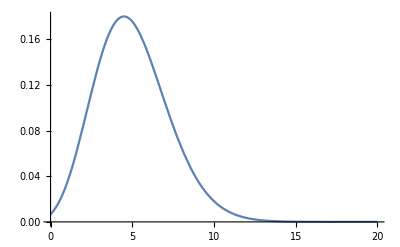

```mathematica
Plot[Exp[-lambda]*lambda^xnew/(xnew!),{xnew,0,20}]
```

## Part D

```mathematica
sample=RandomInteger[PoissonDistribution[5],10^4];
```

```mathematica
samplemean=N[Mean[sample]]
```

5.002

```mathematica
sigma=N[StandardDeviation[sample]]
sigmasquared=N[StandardDeviation[sample]]^2
```

2.21614

4.91129

```mathematica
(* They match the graphs above! *)
```

## Part E

```mathematica
samplemean^(.5)
```

2.23652

```mathematica
sigma
```

2.21614

```mathematica
samplemean^(.5)/sigma
```

1.00919

```mathematica
(* sample mean is the mean of the sample. Sigma is the Standard Deviation. 
I took the square root of the sample mean and found that it was very close to sigma *)
```